#### Valores experimentales del silicio

```mathematica
hb=6.582119569*10^(-16);
```

```mathematica
datos0=Import["C:\\Users\\Nanoplasmonics\\Documents\\GitHub\\Tesis-de-Licenciatura\\Programas\\ParteIm.csv"];
(*Se eliminan los encabezados de los datos*)
datos1=Drop[datos0,1];
(*Se interpolan los datos de la parte imaginaria*)
parteIm=Drop[datos1[[All,2]],{1,20}];
(*Se toma a la primera columna como el vector de energía*)
omega=Drop[datos1[[All,1]],{1,20}];
```

```mathematica
parteReKK1=kkrebook[omega,parteIm];
parteReSSKK1=sskkrebook[omega,parteIm,1.65,19.3548];
parteImKK1=kkimbook[omega,parteReKK1];
```

Set::setraw: Cannot assign to raw object 0.55.

Set::setraw: Cannot assign to raw object 0.6.

Set::setraw: Cannot assign to raw object 0.65.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

Set::setraw: Cannot assign to raw object 0.55.

Set::setraw: Cannot assign to raw object 0.6.

Set::setraw: Cannot assign to raw object 0.65.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

Set::setraw: Cannot assign to raw object 0.55.

Set::setraw: Cannot assign to raw object 0.6.

Set::setraw: Cannot assign to raw object 0.65.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

```mathematica
Clear[selfconsbook]
```

```mathematica
prueba=selfconsbook[omega,parteReKK1,parteIm,1,0.3];
```

Set::setraw: Cannot assign to raw object 0.55.

Set::setraw: Cannot assign to raw object 0.6.

Set::setraw: Cannot assign to raw object 0.65.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

```mathematica
Transpose[{omega,parteReKK1}]
```

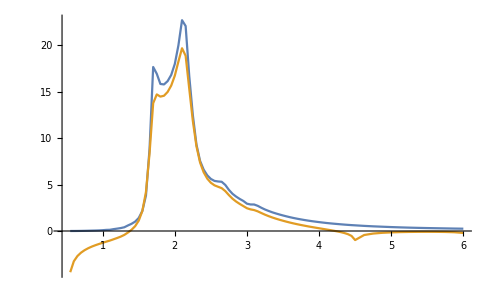

```mathematica
ListLinePlot[{Transpose[{omega,parteIm}],Transpose[{omega,prueba[[2]]}]},PlotRange->All]
```

## Modelo de Drude

```mathematica
omegaMin=2; (*valor mínimo de energía*)
omegaMax=8; (*valor máximo de energía*)
omega10=Range[0.1,10,0.01];(*rango de energías*)
omegaPAl=5.142; (*frecuencia de plasma Al*)
gammaAl=0.147; (*constante de amortuguamiento Al*)
```

```mathematica
(*Se define el modelo de drude*)
epsDrude[ω_,ωp_,γ_]:=1-((ωp)^2/(ω*(ω+ I γ)))
epsLorentz[A_,ω_,ω0_,γ_]:=1+A^2/(ω0^2-ω^2-I*(γ ω))
(*Se define la parte real y la imaginaria del índice de refracción*)
epsImagDrude[energy_,omegaP_,gamma_]:=Im[epsDrude[energy,omegaP,gamma]];
epsReDrude[energy_,omegaP_,gamma_]:=Re[epsDrude[energy,omegaP,gamma]];

epsImagLorentz[A_,ω_,ω0_,γ_]:=Im[epsLorentz[A,ω,ω0,γ]];
epsReLorentz[A_,ω_,ω0_,γ_]:=Re[epsLorentz[A,ω,ω0,γ]];
```

```mathematica
realLorentz=Table[{omega,epsReLorentz[2,omega,omegaPAl,gammaAl]},{omega,0.1,10,0.01}];
imagLorentz=Table[{omega,epsImagLorentz[2,omega,omegaPAl,gammaAl]},{omega,0.1,10,0.01}];
```

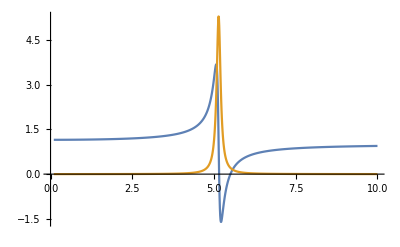

```mathematica
ListLinePlot[{realLorentz,imagLorentz},PlotRange->All]
```

```mathematica
omegas1=Range[0.1,4,0.01];
realLorentz1=Table[{omega,epsReLorentz[0.1,omega,omegaPAl,gammaAl]},{omega,omegas1}];
imagLorentz1=Table[{omega,epsImagLorentz[0.1,omega,omegaPAl,gammaAl]},{omega,omegas1}];
parteReKK1Lorentz=kkrebook[omegas1,imagLorentz1[[All,2]]];
parteImKK1Lorentz=kkimbook[omegas1,realLorentz1[[All,2]]];
omegas2=Range[0.1,5,0.01];
realLorentz2=Table[{omega,epsReLorentz[0.1,omega,omegaPAl,gammaAl]},{omega,omegas2}];
imagLorentz2=Table[{omega,epsImagLorentz[0.1,omega,omegaPAl,gammaAl]},{omega,omegas2}];
parteReKK2Lorentz=kkrebook[omegas2,imagLorentz2[[All,2]]];
parteImKK2Lorentz=kkimbook[omegas2,realLorentz2[[All,2]]];
omegas3=Range[0.1,7,0.01];
realLorentz3=Table[{omega,epsReLorentz[0.1,omega,omegaPAl,gammaAl]},{omega,omegas3}];
imagLorentz3=Table[{omega,epsImagLorentz[0.1,omega,omegaPAl,gammaAl]},{omega,omegas3}];
parteReKK3Lorentz=kkrebook[omegas3,imagLorentz3[[All,2]]];
parteImKK3Lorentz=kkimbook[omegas3,realLorentz3[[All,2]]];
omegas4=Range[0.1,10,0.01];
realLorentz4=Table[{omega,epsReLorentz[0.1,omega,omegaPAl,gammaAl]},{omega,omegas4}];
imagLorentz4=Table[{omega,epsImagLorentz[0.1,omega,omegaPAl,gammaAl]},{omega,omegas4}];
parteReKK4Lorentz=kkrebook[omegas4,imagLorentz4[[All,2]]];
parteImKK4Lorentz=kkimbook[omegas4,realLorentz4[[All,2]]];
omegas5=Range[0.1,15,0.01];
realLorentz5=Table[{omega,epsReLorentz[0.1,omega,omegaPAl,gammaAl]},{omega,omegas5}];
imagLorentz5=Table[{omega,epsImagLorentz[0.1,omega,omegaPAl,gammaAl]},{omega,omegas5}];
parteReKK5Lorentz=kkrebook[omegas5,imagLorentz5[[All,2]]];
parteImKK5Lorentz=kkimbook[omegas5,realLorentz5[[All,2]]];
```

```mathematica
listImag={imagLorentz5,Transpose[{omegas1,parteImKK1Lorentz}],Transpose[{omegas2,parteImKK2Lorentz}],Transpose[{omegas3,parteImKK3Lorentz}],Transpose[{omegas4,parteImKK4Lorentz}],Transpose[{omegas5,parteImKK5Lorentz}]};
listRe={realLorentz5,Transpose[{omegas1,parteReKK1Lorentz}],Transpose[{omegas2,parteReKK2Lorentz}],Transpose[{omegas3,parteReKK3Lorentz}],Transpose[{omegas4,parteReKK4Lorentz}],Transpose[{omegas5,parteReKK5Lorentz}]};
```

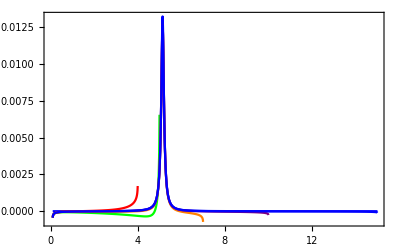
-Graphics--Graphics--Graphics-

```mathematica
Labeled[ListLinePlot[listImag,PlotRange->All,PlotStyle->{Blue,Red,Green,Orange,Purple},Frame->True,
FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.5],FrameTicks->{{Automatic,None},{Automatic,None}},ImagePadding->{{50,35},{25,10}}],{Style[MaTeX["\\varepsilon''(\omega)"],Magnification->1.5],Style[MaTeX["\hbar\omega\: [\mbox{eV}]"],Magnification->1.5]},{Left,Bottom},Spacings->{-0.7,0},RotateLabel->True]
```

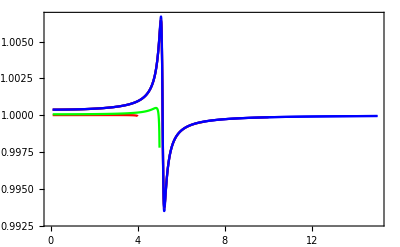
-Graphics--Graphics--Graphics-

```mathematica
Labeled[ListLinePlot[listRe,PlotRange->All,PlotStyle->{Blue,Red,Green,Orange,Purple},Frame->True,
FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.5],FrameTicks->{{Automatic,None},{Automatic,None}},ImagePadding->{{50,35},{25,10}}],{Style[MaTeX["\\varepsilon'(\omega)"],Magnification->1.5],Style[MaTeX["\hbar\omega\: [\mbox{eV}]"],Magnification->1.5]},{Left,Bottom},Spacings->{-0.7,0},RotateLabel->True]
```

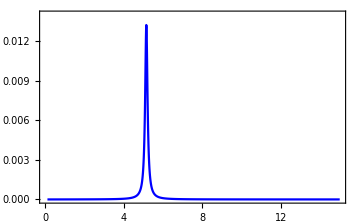
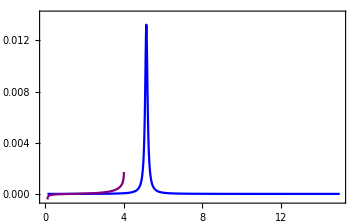
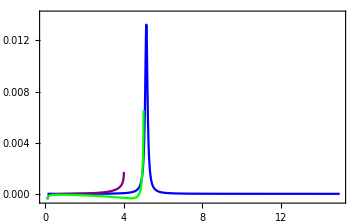
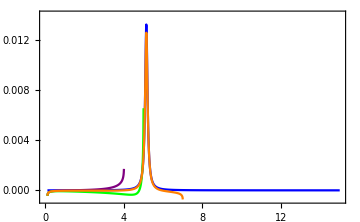
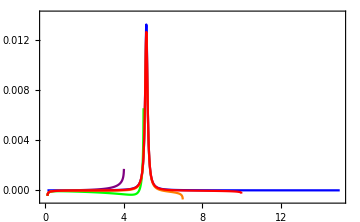
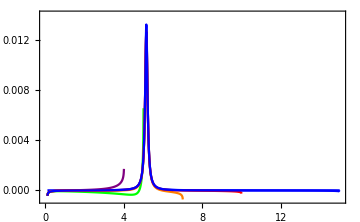
{-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-}

```mathematica
algo = Labeled[ListLinePlot[listImag[[1;;#]],PlotRange->{{0,15},{Automatic,0.014}},ImageSize->Medium,PlotStyle->{Blue,Purple,Green,Orange,Red},Frame->True,
FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.5],FrameTicks->{{Automatic,None},{Automatic,None}},ImagePadding->{{50,35},{25,10}}],{Style[MaTeX["\\varepsilon''(\omega)"],Magnification->1.5],Style[MaTeX["\hbar\omega\: [\mbox{eV}]"],Magnification->1.5]},{Left,Bottom},Spacings->{-0.7,0},RotateLabel->True]&/@Range[1,Length[listImag]]
```

```mathematica
Export["lorentzKKIm.svg",algo]
```

lorentzKKIm.svg

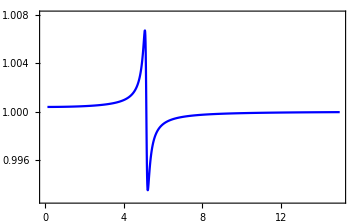
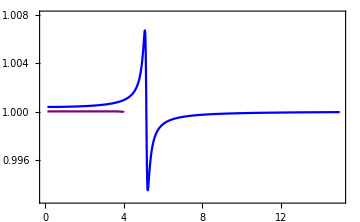
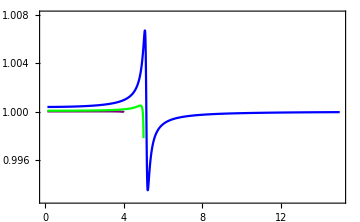
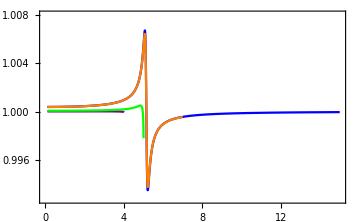
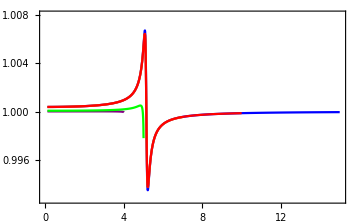
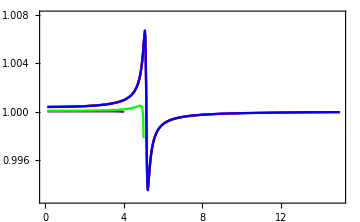
{-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-,-Graphics--Graphics--Graphics-}

```mathematica
algo2= Labeled[ListLinePlot[listRe[[1;;#]],PlotRange->{{0,15},{Automatic,1.008}},ImageSize->Medium,PlotStyle->{Blue,Purple,Green,Orange,Red},Frame->True,
FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.5],FrameTicks->{{Automatic,None},{Automatic,None}},ImagePadding->{{50,35},{25,10}}],{Style[MaTeX["\\varepsilon'(\omega)"],Magnification->1.5],Style[MaTeX["\hbar\omega\: [\mbox{eV}]"],Magnification->1.5]},{Left,Bottom},Spacings->{-0.7,0},RotateLabel->True]&/@Range[1,Length[listRe]]
```

```mathematica
Export["lorentzKKRe.svg",algo2]
```

lorentzKKRe.svg

```mathematica
Export["listRe.gif",algo2,"DisplayDurations"->1/2]
Export["listImag.gif",algo,"DisplayDurations"->1/2]
```

listRe.gif

listImag.gif

```mathematica
SetDirectory["C:\\Users\\Nanoplasmonics\\Documents\\GitHub\\Tesis-de-Licenciatura\\Figuras"]
```

C:\Users\Nanoplasmonics\Documents\GitHub\Tesis-de-Licenciatura\Figuras

```mathematica
listImagKK={Transpose[{datosLambda,kk28im}],Transpose[{omega10,parteImKK28}]};
listReKK={Transpose[{datosLambda,kk28re}],Transpose[{omega10,parteReKK28}]};
```

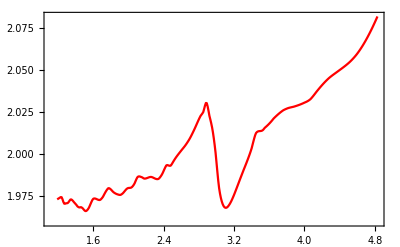
-Graphics--Graphics--Graphics-

```mathematica
eps28ReExp=Labeled[ListLinePlot[Table[{x,eps28Re[x]},{x,1.19,4.83,0.01}],PlotRange->All,PlotStyle->{Red,Style[Red,Dashed]},Frame->True,
FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.5],FrameTicks->{{Automatic,None},{Automatic,None}},ImagePadding->{{50,35},{25,10}}],{Style[MaTeX["\\varepsilon'(\omega)"],Magnification->1.5],Style[MaTeX["\hbar\omega\: [\mbox{eV}]"],Magnification->1.5]},{Left,Bottom},Spacings->{-0.7,0},RotateLabel->True]
```

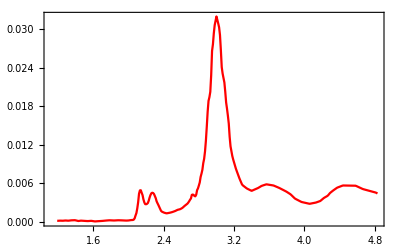
-Graphics--Graphics--Graphics-

```mathematica
eps28ImExp=Labeled[ListLinePlot[Table[{x,eps28Im[x]},{x,1.19,4.83,0.01}],PlotRange->All,PlotStyle->{Red,Style[Red,Dashed]},Frame->True,
FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.5],FrameTicks->{{Automatic,None},{Automatic,None}},ImagePadding->{{50,35},{25,10}}],{Style[MaTeX["\\varepsilon''(\\omega)"],Magnification->1.5],Style[MaTeX["\\hbar\\omega\: [\\mbox{eV}]"],Magnification->1.5]},{Left,Bottom},Spacings->{-0.7,0},RotateLabel->True]
```

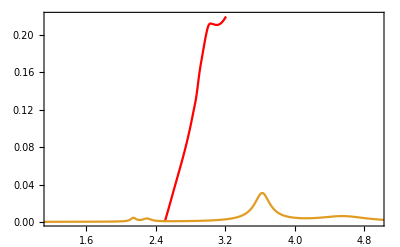
-Graphics--Graphics--Graphics-

```mathematica
eps28ImKK=Labeled[ListLinePlot[listImagKK,PlotRange->{{1.19,4.95},{0,0.22}},PlotStyle->{Red,Style[Red,Dashed]},Frame->True,
FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.5],FrameTicks->{{Automatic,None},{Automatic,None}},ImagePadding->{{50,35},{25,10}}],{Style[MaTeX["\\varepsilon''(\omega)"],Magnification->1.5],Style[MaTeX["\hbar\omega\: [\mbox{eV}]"],Magnification->1.5]},{Left,Bottom},Spacings->{-0.7,0},RotateLabel->True]
```

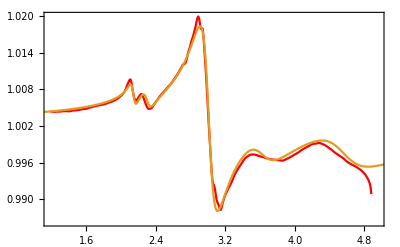
-Graphics--Graphics--Graphics-

```mathematica
eps28ReKK=Labeled[ListLinePlot[listReKK,PlotRange->{{1.19,4.95},{Automatic,Automatic}},PlotStyle->{Red,Style[Red,Dashed]},Frame->True,
FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.5],FrameTicks->{{Automatic,None},{Automatic,None}},ImagePadding->{{50,35},{25,10}}],{Style[MaTeX["\\varepsilon''(\omega)"],Magnification->1.5],Style[MaTeX["\hbar\omega\: [\mbox{eV}]"],Magnification->1.5]},{Left,Bottom},Spacings->{-0.7,0},RotateLabel->True]
```

```mathematica
Export["eps28ReExp.svg",eps28ReExp]
Export["eps28ImExp.svg",eps28ImExp]
Export["eps28ReKK.svg",eps28ReKK]
Export["eps28ImKK.svg",eps28ImKK]
```

eps28ReExp.svg

eps28ImExp.svg

eps28ReKK.svg

eps28ImKK.svg

#### Valores experimentales del oro

```mathematica
au=Import["C:\\Users\\Poh\\Documents\\GitHub\\Servicio-Social\\Notebooks Mathematica\\Funciones dieléctricas\\Oro Johnson.csv"];
```

```mathematica
nau1=Drop[Drop[au,{51,101}],1];
kau1=Drop[au,{1,52}];
λAu=nau1[[All,1]]*1000; (*λ en um*)
ωAu=h c/λAu; (*eV*)
nau=nau1[[All,2]];
kau=kau1[[All,2]];
```

```mathematica
ωAu
```

{6.60298,6.47547,6.35279,6.22529,6.10281,5.98505,5.85512,5.73337,5.60389,5.48497,5.36403,5.23281,5.11418,4.98273,4.86358,4.74274,4.61398,4.49366,4.36252,4.24316,4.1233,3.99324,3.87235,3.74269,3.62248,3.50282,3.37238,3.25216,3.12204,3.00194,2.882,2.75161,2.63195,2.50192,2.38184,2.26158,2.13142,2.01151,1.88127,1.76111,1.64114,1.51102,1.39092,1.26087,1.14035,1.02031,0.890668,0.770621,0.640527}

```mathematica
nInterpFunction=Interpolation[Transpose[{ωAu,nau}]];
kInterpFunction=Interpolation[Transpose[{ωAu,kau}]];
```

```mathematica
nAu=Table[nInterpFunction[x],{x,0.65,6.6,0.01}];
kAu=Table[kInterpFunction[x],{x,0.65,6.6,0.01}];
energy=Range[0.65,6.6,0.01];
```

```mathematica
nInterpFunction[3]
```

1.45997

```mathematica
parteReKKAu=kkrebook[energy,kAu];
parteImKKAu=kkimbook[energy,parteReKKAu];
pruebaAu10=selfconsbook[energy,parteReKKAu,kAu,20,0.5];
pruebaSelf=sskkrebook[energy,kAu,3,nInterpFunction[3]];
```

Set::setraw: Cannot assign to raw object {0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,«586»}.

Set::setraw: Cannot assign to raw object 13.5607.

Set::setraw: Cannot assign to raw object 13.3351.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

Set::setraw: Cannot assign to raw object {0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,«586»}.

Set::setraw: Cannot assign to raw object {22.4847,17.8861,15.5244,13.9228,12.7085,11.731,10.9141,10.2139,9.6025,9.06121,«586»}.

Set::setraw: Cannot assign to raw object {0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,«586»}.

Set::setraw: Cannot assign to raw object {22.4847,17.8861,15.5244,13.9228,12.7085,11.731,10.9141,10.2139,9.6025,9.06121,«586»}.

Set::setraw: Cannot assign to raw object 13.5607.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

Set::setraw: Cannot assign to raw object {0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,«586»}.

Set::setraw: Cannot assign to raw object 13.5607.

Set::setraw: Cannot assign to raw object 13.3351.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

Set::setraw: Cannot assign to raw object {0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,«586»}.

Set::setraw: Cannot assign to raw object 13.5607.

Set::setraw: Cannot assign to raw object 13.3351.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

Set::setraw: Cannot assign to raw object {0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,«586»}.

Set::setraw: Cannot assign to raw object {22.4847,17.8861,15.5244,13.9228,12.7085,11.731,10.9141,10.2139,9.6025,9.06121,«586»}.

Set::setraw: Cannot assign to raw object {0.65,0.66,0.67,0.68,0.69,0.7,0.71,0.72,0.73,0.74,«586»}.

Set::setraw: Cannot assign to raw object {22.4847,17.8861,15.5244,13.9228,12.7085,11.731,10.9141,10.2139,9.6025,9.06121,«586»}.

Set::setraw: Cannot assign to raw object 13.5607.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

2

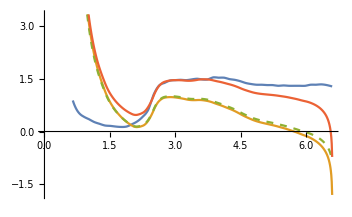

```mathematica
ListLinePlot[{Transpose[{energy,nAu}],Transpose[{energy,parteReKKAu}],Style[Transpose[{energy,pruebaAu10[[1]]}],Dashed],Transpose[{energy,pruebaSelf}]}]
```